```mathematica
$PlotTheme->"Scientific"
```

Automatic→Scientific

First initialize parameters.

```mathematica
timeconstant=R=4; 
threshold=10; (*Experimentally calculated*)
T=10;
```

## Learning to simulate neural network

```mathematica
{net,indexST, voltageFunctions, TableST}=netSim[1,1,10,{6},0];
```

```mathematica
net
```

-Graphics-

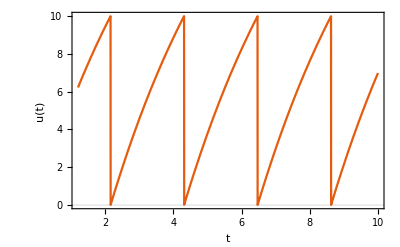

```mathematica
Plot[u[t]/.voltageFunctions,{t,1.2,10},FrameLabel->{t,u[t]} ,PlotRange->Full]
```

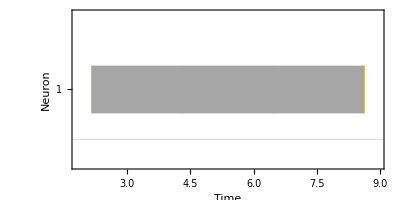

The firing rate of this neuron is: {2/5}

```mathematica
spktrnF[TableST,ImageSize->400,AspectRatio->1/2,ChartStyle->"SolarColors",FrameStyle->16,FrameLabel->{"Time","Neuron",None,None}]
Print["The firing rate of this neuron is: " , firingRate[TableST,T]]
```

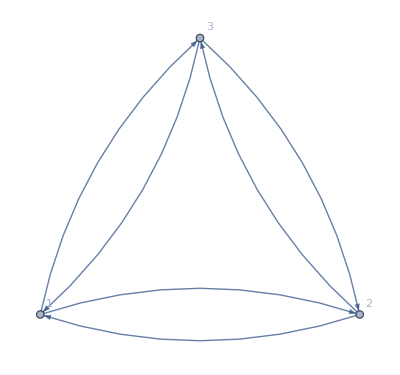

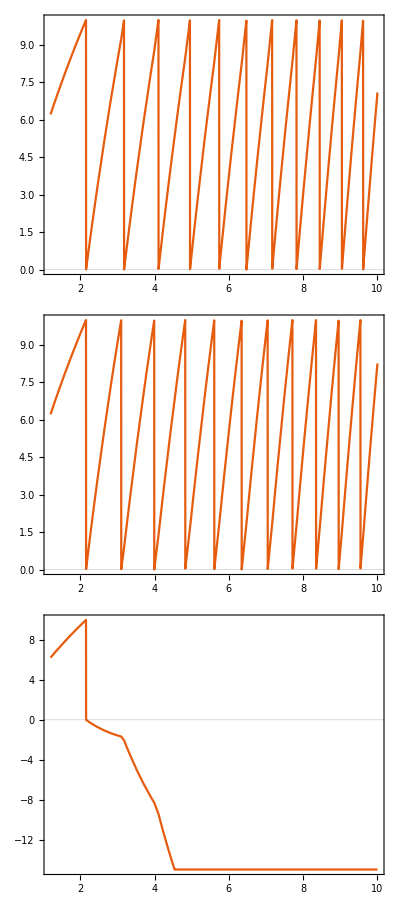

```mathematica
SeedRandom[0];
{net,indexST, voltageFunctions, TableST}=netSim[3,0.5,10,{6,6,6},0];
net
Table[Plot[u[t]/.voltageFunctions⟦i⟧,{t,1.2,10},PlotRange->Full],{i,1,3}]//TableForm
```

Note that the membrane potential does not decrease below -15 mV. This has a biological explanation, because a neuron’s membrane potential cannot be below the resting potential of potassium voltage, which is around -80mV. Since graphs are shifted by +65 mV , therefore v_K=-15mV.

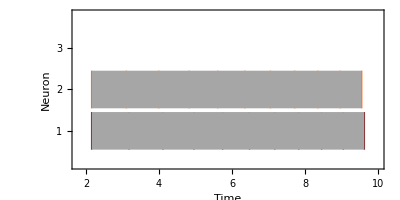

The firing rate of the neurons is: {11/10,11/10,1/10}

```mathematica
spktrnF[TableST,ImageSize->400,AspectRatio->1/2,ChartStyle->"SolarColors",FrameStyle->16,FrameLabel->{"Time","Neuron",None,None}]
Print["The firing rate of the neurons is: " , firingRate[TableST,T]]
```

-Graphics-

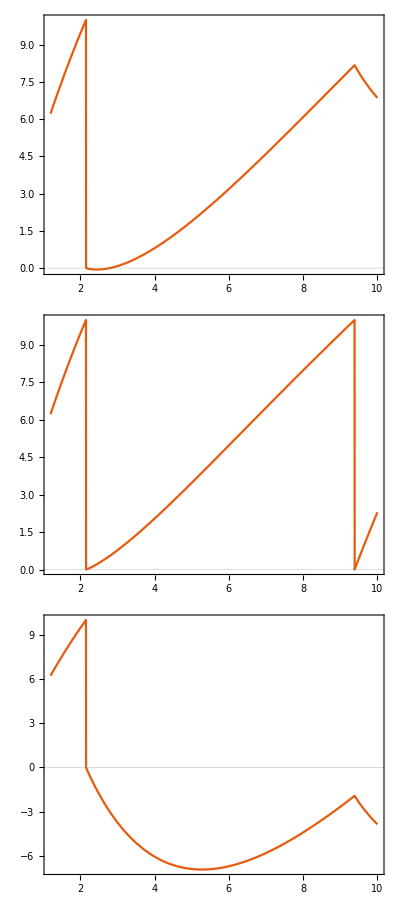

```mathematica
SeedRandom[0];
{net,indexST, voltageFunctions, TableST}=netSim[3,0.5,10,{6,6,6},-1];
net
Table[Plot[u[t]/.voltageFunctions⟦i⟧,{t,1.2,10},PlotRange->Full],{i,1,3}]//TableForm
```

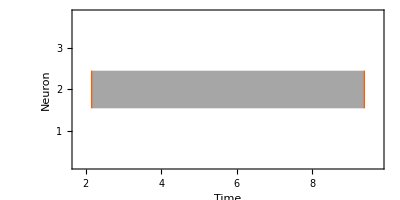

The firing rate of the neurons is: {1/10,1/5,1/10}

```mathematica
spktrnF[TableST,ImageSize->400,AspectRatio->1/2,ChartStyle->"SolarColors",FrameStyle->16,FrameLabel->{"Time","Neuron",None,None}]
Print["The firing rate of the neurons is: " , firingRate[TableST,T]]
```